### supervised learning

#### example1

```mathematica
trainingset={1->1.3,2->2.4,3->6.4,4->10.1};
```

```mathematica
p=Predict[trainingset,Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
p[1.555]
```

2.20603

#### example2

```mathematica
bhdata=ExampleData[{"MachineLearning","BostonHomes"},"TrainingData"];
```

```mathematica
Length@bhdata
```

338

```mathematica
RandomSample[bhdata,1]
```

{{4.54192,0,18.1,0,0.77,6.398,88,2.5182,24,666,20.2,374.56,7.79}→25}

```mathematica
Flatten/@List@@@ bhdata[[1;;3]]
```

{{0.02731,0,7.07,0,0.469,6.421,78.9,4.9671,2,242,17.8,396.9,9.14,21.6},{0.02729,0,7.07,0,0.469,7.185,61.1,4.9671,2,242,17.8,392.83,4.03,34.7},{0.03237,0,2.18,0,0.458,6.998,45.8,6.0622,3,222,18.7,394.63,2.94,33.4}}

```mathematica
Export[System]
```

#### example3

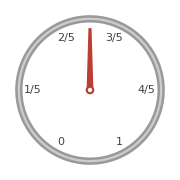

```mathematica
AngularGauge[.5]
```

```mathematica
Head@%10
```

Graphics

```mathematica
trainingset=(Image[AngularGauge@#]->#)&/@RandomReal[1,100];
```

```mathematica
RandomSample[trainingset,2]
```

{-Graphics-→0.572429,-Graphics-→0.613175}

```mathematica
predictor=Predict@trainingset
```

PredictorFunction[…]

```mathematica
Row[{AngularGauge[Dynamic[t]],Style["-> ",Large],Dynamic[Labeled[AngularGauge[predictor[Image[AngularGauge[t]]]],"(predicted value)"]]},BaseStyle->FontFamily->"Sans Serif"]
```

->

```mathematica
Dynamic[Labeled[AngularGauge[#],"(predicted value = "<>ToString@#<>")"]&@predictor[Image[AngularGauge[t]]]]
```

#### example5

```mathematica
spf=SequencePredict[{{1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4}}]
```

SequencePredictorFunction[…]

```mathematica
spf[{1,2}]
```

3

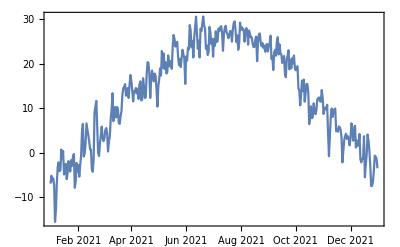

```mathematica
DateListPlot[WeatherData["Beijing","MeanTemperature",{{2021,1,1},{2021,12,31},"Day"}],Joined->True]
```

```mathematica
plot = WeatherData["Beijing","MeanTemperature",{{2021,1,1},{2021,12,31},"Day"}]
```

TimeSeries[…]

```mathematica
temperature = Normal[plot[[2,1,1]]][[All,1]]
```

{-7,-5.22,-6.44,-5.83,-7.28,-15.61,-12.89,-6.94,-3.22,-2.22,-4.22,-3.94,0.67,-1.28,0.33,-4.94,-3.67,-2.56,-6,-4.61,-1.94,-3.72,-4.28,-1.72,-3,-0.89,-0.33,-7.94,-6.56,-2.33,-4.28,-2.83,-5.44,-2.89,-0.78,4.5,6.44,-0.89,-0.22,2,6.56,2.61,0.72,0.67,-3.78,-4.33,-1.5,9,11.61,5.67,-0.11,-0.78,2.06,3.78,5.83,3.28,2.56,3.22,5.06,5.5,4.39,0.22,2.5,3.61,7.56,9.56,13.33,7.06,10,10.22,7.89,10.22,9.89,6.61,6.44,8.22,9.28,13.06,14.44,14.78,15.39,12.78,14.11,14.5,12.28,15.28,17.44,16.06,13.83,11.5,13.78,13.56,14.5,13.28,14.33,12.06,15.33,16,11.72,11.94,16.72,14.89,12.28,12.39,17.56,20.33,20.17,17.72,12.28,16.5,18.44,17.11,16,17.78,17.22,14.17,10.33,14.89,16.5,18.94,17.33,22.83,19.11,22.28,18.78,20.33,17.78,18.06,21.83,19.39,20.61,18.83,23.78,26.44,25.56,23.83,24.67,24.89,21.61,19.67,21.06,19.22,21.28,23.11,22,21.28,15.44,21.56,20.67,23.56,23.17,28.67,27.39,23.67,25.11,21.39,25.94,28.33,30.56,26.89,23.33,25.17,21.39,27.83,27.33,29,30.61,28.56,27.89,23.33,24.06,21.94,22.67,28.28,27,24.39,25.56,21.56,25.5,24,27.28,24.83,25.06,27.89,27.33,28.17,28.44,26.83,22.89,26.56,28,28.5,27.11,26.61,25.72,26.33,27.33,27.22,24.94,27.78,29.11,29.5,27.5,24.83,26.39,23.11,24.5,29.22,27.61,28.22,27.61,27.72,24.94,26.72,28,27.11,24.28,27.44,26.67,25.94,25.89,24.5,23.72,23.78,25.44,26.06,20.56,24.83,26.56,26.78,24.72,23.94,24.61,23.56,24.06,22.67,24.06,24.44,22.72,24,24.56,26.28,21.06,21.61,18.56,22.5,23.11,21.78,24.89,25.94,22.06,24.33,22.28,22.06,20.17,20.83,21.72,17.83,16.94,21,21.78,23,18.72,20.89,18.94,21.22,20.06,21.83,19.11,18.5,19.28,19.39,14.44,14,10.61,13.17,16.17,13.83,16.39,11.44,13.33,15.44,15.39,13.5,6.39,8.22,10.39,7.72,7.94,11.06,9.56,8.61,9.5,11.94,12.22,12.39,11.56,11.44,14.06,12.28,8.67,9.72,10.11,9.72,10.72,4.33,-0.83,3.56,7.94,9.89,8,9,9.72,9.89,4.78,5.17,4.67,5.89,5.67,5.06,3.33,-2.22,0.39,2.78,3.72,4.22,3.06,3.67,3.28,1.61,3.17,6.56,5.78,2.67,3.78,6,1.11,2.72,1.5,2.11,4.17,-1.5,-2.22,-1.39,-1.33,3.67,-5.56,-2.78,-0.44,4.06,2.72,0.44,-3,-7.56,-7.5,-6.5,-4.11,-0.72,-0.94,-1.39,-3.56}

```mathematica
spf2 = SequencePredict[{temperature}]
```

SequencePredictorFunction[…]

```mathematica
spf2[{20}]
```

12.28

```mathematica
Positive[1]
```

True

```mathematica
acf=ActiveClassification[Positive,Interval[{-10,10}]]["ClassifierFunction"]
```

ClassifierFunction[…]

```mathematica
acf@-0.00001
```

True

```mathematica
ac0 = ActiveClassification[#>5&,Interval[{0,10}]]
```

ActiveClassificationObject[…]

```mathematica
c = ac0["ClassifierFunction"]
```

ClassifierFunction[…]

```mathematica
c@7
```

True

#### example6

```mathematica
cf1=Classify[{1.82->"male",1.90->"male",1.75->"male",1.55->"male",1.6->"female"}];
```

```mathematica
cf1[1.6]
```

male

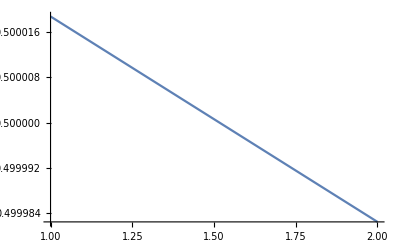

```mathematica
Plot[cf1[x,{"Probability","female"}],{x,1,2}]
```

```mathematica
cf1[1.6,"Probabilities",ClassPriors-><|"male"->.5,"female"->.5|>]
```

<|female→0.714283,male→0.285717|>

```mathematica
cf1[1.6,"Probabilities"]
```

<|female→0.499997,male→0.500003|>

```mathematica
trainigset={1->"healthy",2->"diseased",3->"healthy",4->"diseased",5->"diseased"};
```

```mathematica
c=Classify@trainigset
```

ClassifierFunction[…]

```mathematica
c[1.5,"Probabilities"]
```

<|diseased→0.26269,healthy→0.73731|>

```mathematica
c[1.5]
```

healthy

```mathematica
c[1.5,UtilityFunction-><|"healthy"-><|"healthy"->1,"diseased"->0|>,"diseased"-><|"healthy"->-2,"diseased"->1|>|>]
```

diseased

```mathematica
c[1.5]
```

healthy

#### example7

```mathematica
NetEncoder["Characters"]["A large cat"]
```

{36,3,79,68,85,74,72,3,70,68,87}

```mathematica
c=Classify[{"the cat is grey"->-Graphics-,"my cat is fast"->-Graphics-,"this dog is scary"->-Graphics-,"the big dog"->-Graphics-},FeatureExtractor->{ToUpperCase,RemoveDiacritics,"SegmentedWords"}]
```

ClassifierFunction[…]

```mathematica
c[{"nice dat","what a cog"}]
```

{-Graphics-,-Graphics-}

```mathematica
planePoints=N[Position[ImageData@-Graphics-,1,{2}]];
```

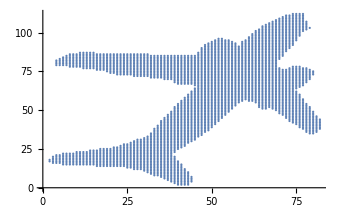

```mathematica
ListPlot@planePoints
```

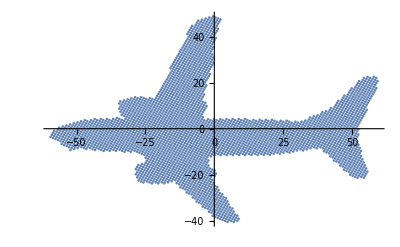

```mathematica
ListPlot@PrincipalComponents@planePoints
```

### dimension reduction

```mathematica
vecs = {{1,2,3},{2,3,5},{3,5,8}};
```

```mathematica
DimensionReduce[vecs,1]
```

{{1.97985},{0.248109},{-2.22796}}

#### unsupervised learning

```mathematica
fe1=FeatureExtraction[{{1.4,"A"},{1.5,"A"},{2.3,"B"},{5.4,"B"}}]
```

FeatureExtractorFunction[…]

```mathematica
fe1[{1.4,"A"}]
```

{-0.768958,1.00001,1.}

```mathematica
img = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
fe=FeatureExtraction[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

FeatureExtractorFunction[…]

```mathematica
question = fe[-Graphics-]
```

{151.467,-91.8606,-0.777854,51.1772,69.5567}

```mathematica
EuclideanDistance[#,question]&/@fe@img
```

{175.474,201.745,183.018,202.774,209.574,220.911}

```mathematica
data = fe@img
```

{{16.9775,1.43448,3.41155,10.0882,21.6653},{8.51811,13.1914,11.7409,12.4947,-17.493},{22.9647,-10.6604,-12.631,-14.1652,-7.76728},{-15.2263,-20.7143,18.8288,-3.86607,-0.117296},{-19.4959,-3.95773,-21.8003,12.8176,-1.52362},{-13.7381,20.7065,0.450046,-17.3692,5.23589}}

```mathematica
Graphics3D@Point@DimensionReduce[data,3]
```

-Graphics3D-

```mathematica
URL@"http://vision.stanford.edu/aditya86/ImageNetDogs/"
```

#### neural network

```mathematica
net=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

```mathematica
net@-Graphics-
```

8

```mathematica
net[-Graphics-,"Probabilities"]
```

<|0→7.28386×10^-13,1→1.8159×10^-16,2→2.15518×10^-12,3→3.2635×10^-12,4→9.74528×10^-15,5→6.61678×10^-10,6→3.45442×10^-13,7→3.57894×10^-20,8→1.,9→2.42621×10^-12|>